# Practical Codes for Storage Systems

# An Introduction to Entanglement Codes

Entanglement codes generate redundant information to protect content against failures in a storage system. The method increases the reliability and also improves performance because it creates multiple paths to read data using combinations of elements stored in the system.

## Simple Entanglement Codes

Simple entanglements create chains of interdependent elements that alternate data represented by a vertex and redundant information represented by an edge.

A visualization of an open entanglement chain. The first and last vertices are virtual elements and do not contain information. The first vertex contains the initial condition of the chain:

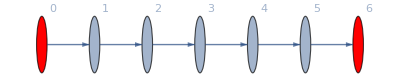

```mathematica
g=Graph[{0 ->1,1->2,2->3,3->4, 4->5,5->6},VertexLabels->"Name",VertexSize->Medium, VertexStyle -> {0 ->Red,6->Red}]
```

### Write data

Vertices represent data. They can store anything, e.g. a digit, numbers, characters, strings or large chunks of data. The only constrain is that all of them must store the same amount of information.

In this example, the chain will store “Hello”. First, we convert the string to character codes:

```mathematica
vertexValues=ToCharacterCode["Hello"]
```

{72,101,108,108,111}

The encoder uses the function BitXor to compute the bitwise XOR of the last two elements of the chain. The input are the vertex being encoded and its incident edge (whose weight was generated during the encoding of its predecessor vertex and contains redundant information derived from all the predecessor vertices).

If the vertex values is known, the encoding process is equivalent to compute the cumulative bitwise XOR operations of the elements of the vertexValues list:

```mathematica
{Apply[Xor,#]&,{True}}
```

{Xor@@#1&,{True}}

```mathematica
CellularAutomaton[{Apply[Xor,#]&,{}},{{False,False,True},True},1]
```

{{True,False,False,True},{False,True,True,False}}

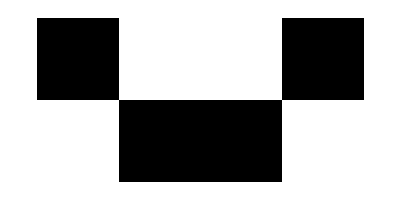

```mathematica
ArrayPlot[Boole[CellularAutomaton[{Apply[Xor,#]&,{}},{{False,False,True},True},1]]]
```

```mathematica
encodedData= FoldList[BitXor,0,vertexValues]
```

{0,72,45,65,45,66}

The list of vertexValues only contains the values for vertices 1-5. Let’s fix it.

To fill the virtual vertices with some content, we add zeros at the first and last position of the list:

```mathematica
vertexValues= Insert[vertexValues,0,{{1},{-1}}]
```

{0,72,101,108,108,111,0}

Now, we can redefine the graph using the new content.

We could describe vertices with associations. The key is the index/label of the vertex and the value contains one element of the vertexValues list:

```mathematica
vertex = AssociationThread[VertexList[g],vertexValues]
```

<|0→0,1→72,2→101,3→108,4→108,5→111,6→0|>

We can visualize the entanglement chain using the vertex weight to store plain data and edge weight to store encoded data:

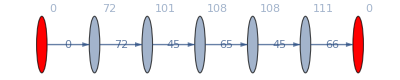

```mathematica
g=Graph[{0->1,1->2,2->3,3->4, 4->5,5->6},VertexSize->Medium,VertexStyle -> {0 ->Red,6->Red},VertexWeight->vertexValues,EdgeWeight-> encodedData,VertexLabels->"VertexWeight",EdgeLabels-> "EdgeWeight"]
```

### Read data

Data can be recovered using nodes or edges

Method 1: Reading plain text from vertices (without decoding)

```mathematica
Row[FromCharacterCode[PropertyValue[{g,#},VertexWeight]]&/@{1,2,3,4,5}]
```

Hello

Method 2: Decoding data from edges. We apply BitXor to pair of values obtained by Partition.

```mathematica
FromCharacterCode[BitXor@@@Partition[encodedData,2,1]]
```

Hello

### Decoding in detail

We can read the content of a node by applying the bitwise XOR to the weight of its two adjacent edges

For example, to read “e” (char code 101) we use the adjacent edges that contain 72 and 45.

```mathematica
FromCharacterCode[BitXor[encodedData[[2]],encodedData[[3]]]]
```

e

We can also recompute the value of an edge. There are two ways depending on the direction we are moving on the chain. In this example, we recomputed encodedData[[3]]:

Moving from left to right:

```mathematica
BitXor[encodedData[[2]],vertexValues[[3]]]
```

45

Moving from right to left:

```mathematica
BitXor[encodedData[[4]],vertexValues[[4]]]
```

45

## Failure Patterns (cmd/alt+4)

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins
derivation
applications
common misunderstandings
recent developments
unanswered questions

Simple Entanglements behavior

Name of a related topic for exploration

Name of another related topics for exploration (repeat as needed)

Authorship information

Vero Estrada-Galinanes

Date of creation

Author email address (please use the email associated with your Wolfram User ID)

MapThread::mptd: Object FE`DynamicModuleVariableList$18 at position {2, 1} in MapThread[FrontEnd`Private`settouch,{FE`DynamicModuleVariableList$18,FE`DynamicModuleVariableList$18}] has only 0 of required 1 dimensions.

FE`ExecuteInDynamicModule::noval: Symbol FE`DynamicModuleVariableList$18 does not have a value.